```mathematica
Clear[f,c]
d=0.2
c=0.3; 
ym = c^(-1/1.5)
k=1
(* x corresponds to z, and y to Beta*) (* for single beta value set yMin=yMax *)

xMin=-0.4;xMax=0.0005;yMin=ym;yMax=ym;
dx=0.001;dy=0.02; 
len = (xMax-xMin)/dx
beta=yMin
(*Create a grid of points*)
grid=Flatten[Table[{x,y},{x,xMin,xMax,dx},{y,yMin,yMax,dy}],1];
fValues=Association[Thread[grid->0]];

(*Iterative solver*)
maxIter=200;
tol=10^-6;

For[iter=1,iter<=maxIter,iter++,fOld=fValues;
(*Ensure fOld has valid interpolation*)fInterp=If[Length[fOld]>0,Interpolation[Normal[KeyValueMap[{#1,#2}&,fOld]],InterpolationOrder->1],Function[{x,y},0]];
(*Update each point in the grid*)newValues=Flatten[Table[Module[{xNew,fLookup},xNew=x*y;(*Check if xNew is in grid,else use interpolation*)fLookup=If[KeyExistsQ[fOld,{xNew,y}],fOld[{xNew,y}],fInterp[xNew,y]];
{{x,y}->c (Exp[ x*y+fLookup]-1)}  ],
  {x,xMin,xMax,dx},{y,yMin,yMax,dy}]];
(*Ensure newValues is a valid list of rules before updating*)If[Length[newValues]>0,fValues=Association[newValues],Break[]];
(*Check for convergence*)If[Max[Abs[Values[fValues]-Values[fOld]]]<tol,Break[]];
(*Debugging step:print maximum value of fValues to track updatesPrint["Iteration: ",iter]*);(*Print["Max(fValues): ",Max[Values[fValues]]]*);]

(*Debugging step:Check range of fValues*)
(*Print["Range of fValues: ",Min[Values[fValues]]," to ",Max[Values[fValues]]];*)

(*Convert fValues to a 2D array for visualization*)
fMatrix=Table[fValues[{x,y}],{x,xMin,xMax,dx},{y,yMin,yMax,dy}];

(*Plot matrix of fValues as a 2D heatmap*)
ListDensityPlot[fMatrix,PlotLabel->"Density Plot of fValues",Frame->True,Axes->True,AxesLabel->{x,y}];

(*Create coordinates for 3D plot:*)xCoords=Table[x,{x,xMin,xMax,dx}];
yCoords=Table[y,{y,yMin,yMax,dy}];

(*Create a grid of {x,y,f(x,y)} for 3D plotting*)
dataForPlot=Flatten[Table[{x,y,fValues[{x,y}]},{x,xMin,xMax,dx},{y,yMin,yMax,dy}],1];

(*Plot the 3D surface using the data*)
Numerical3D = ListPointPlot3D[dataForPlot,PlotStyle->Directive[PointSize[0.015],Blue],PlotLabel->"3D Plot of f(x, y)",AxesLabel->{"x","y","f(x, y)"}]
```

0.2

2.23144

1

400.5

2.23144

Interpolation::inhr: Requested order is too high; order has been reduced to {1,0}.

InterpolatingFunction::dmval: Input value {-0.892577,2.23144} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.890346,2.23144} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.888114,2.23144} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Interpolation::inhr: Requested order is too high; order has been reduced to {1,0}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

ListDensityPlot::gmat: {{-0.211892,-0.211647,-0.211401,-0.211155,-0.210908,-0.21066,-0.210411,-0.210162,-0.209912,-0.209661,«391»}} is not a rectangular array larger than 2 x 2.

-Graphics3D-

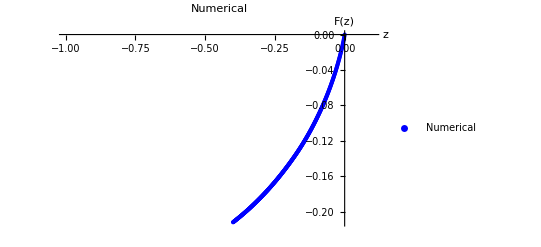

```mathematica
(*Plot numerical solution in 2D*)
Newlist = {Transpose[dataForPlot][[1]],Transpose[dataForPlot][[3]]};
validData=Select[Transpose[Newlist],FreeQ[#,Overflow[]]&];
{xValues,yValues}=Transpose[validData];

NumericalSol = ListPlot[Transpose[{xValues,yValues}],PlotStyle->{Blue,Thick},AxesLabel->{"z","F(z)"},PlotLabel->"Numerical",
PlotRange->{{-1,0.1},Automatic},PlotLegends->{"Numerical"}]
```

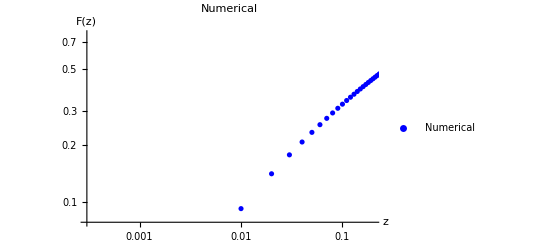

```mathematica
LogNumericalSol = ListLogLogPlot[Transpose[{-xValues,-yValues}],PlotStyle->{Blue,Thick},AxesLabel->{"z","F(z)"},PlotLabel->"Numerical",
PlotRange->{{Min[xValues]-0.2,Max[xValues]+0.2},Automatic},PlotLegends->{"Numerical"},Epilog->{Directive[Blue,Dashed,Thick],Line[{{c-1-Log[c],-1},{c-1-Log[c],1}}]}]
```

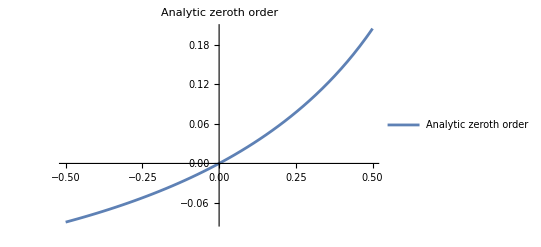

```mathematica
(*plot analytic solution at beta=1*)
ψ[z_]:=-Exp[z-c+Log[c]]
AnalyticSol = Plot[-c-ProductLog[0,ψ[z]],{z,-0.5,0.5},PlotLabel->"Analytic zeroth order",PlotLegends->{"Analytic zeroth order"}]
```

```mathematica
Limit[ProductLog[0,ψ[-I z]]-ProductLog[0,ψ[I z]],z->9π/2+0.7]
```

0.+0.325963 ⅈ

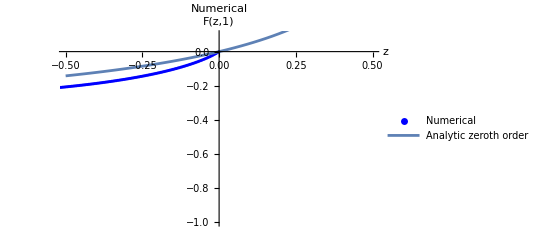

```mathematica
(*Compare analytic at beta=1 with numerical solution for given beta*)
Show[NumericalSol,AnalyticSol,PlotLegends->{"Numerical","Analytic"},AxesLabel->{"z","F(z,1)"},PlotRange->{{-0.5,0.5},{-1,0.1}}]
```

```mathematica
(*plot the 0th+1st order analytic correction for given beta *)
beta=yMin
AnalyticSolbeta = Plot[-c-ProductLog[0,ψ[z]]+(beta-1)*(-z*ProductLog[0,ψ[z]]/(1+ProductLog[0,ψ[z]])^2),{z,-1,0.5},PlotLabel->"first order Analytic beta=yMin",PlotLegends->{"Analytic first order"}];
```

100.

```mathematica
beta=yMin
p[z_]= -Exp[-1+z]
AnalyticSold = Plot[-1-ProductLog[0,p[z]]+(d)*(1-z ProductLog[0,p[z]]/(k*(1+ProductLog[0,p[z]])^2)),{z,-1,1},PlotLabel->"first order Analytic beta=yMin",PlotLegends->{"Analytic first order d"},PlotStyle->Orange];
```

100.

Set::write: Tag Real in 1.5[z_] is Protected.

-ⅇ^(-1+z)

```mathematica
beta=yMin
ψ0 =-c Exp[-c] 
AnalyticSolpsi = Plot[-c-ProductLog[0,ψ[z](1+(beta-1)Log[ψ[z]/ψ0]/(1+ProductLog[0,ψ[z]]))],{z,-1,0.3},PlotLabel->"first order Analytic beta=yMin",PlotLegends->{"Analytic first order psi"},PlotStyle->Green];
```

100.

-0.000999

-101.494

-118.732

-7152.65

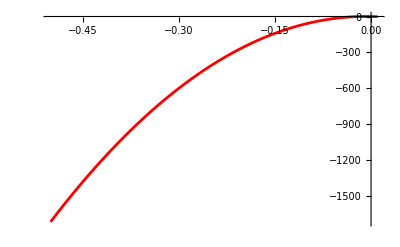

General::munfl: Internal`AbsSquare[-3.16933×10^-162] is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
a0 = 1/Log[c];
a1 =  -Exp[4.62](*-Exp[1.49]*)(*(1/(1-g)+g(1-g)-Log[Abs[-(((-1+g)^2 g Log[g]^2)/(1-2 g+g^2+4 Log[g]-3 g Log[g]-5 g^2 Log[g]+6 g^3 Log[g]-2 g^4 Log[g]+4 Log[g]^2+2 g Log[g]^2-8 g^2 Log[g]^2+2 g^3 Log[g]^2+5 g^4 Log[g]^2-4 g^5 Log[g]^2+g^6 Log[g]^2))]]/Log[g])/.{g->c}*)
a2  =0.5 a0^2/(c-1);
(*a3 = (-2a2 Log[c]+a0(a1))/(c-1);*)
a3= (a0+a0 a1-a0^2 Log[c]-2 a2 Log[c])/(-1+c)
(*a4 = (a2 Log[c]^2/c-Log[c]a3+a1^2/2)/(c-1);*)
a4= 1/(2 (-1+c))(1+2 a1+a1^2-2 a0 Log[c]-2 a0 a1 Log[c]-2 a3 Log[c]+a0^2 Log[c]^2+2 a2 Log[c]^2)
(*+a1 z+a2 z^2 Log[Abs[z]]^2+a3 z^2 Log[Abs[z]]+a4 z^2*)
 Bc10=Plot[-a0 Abs[z]^k Log[Abs[z]],{z,-0.5,0.01},PlotStyle->Red];
Bc11 =Plot[-a0 Abs[z]^k Log[Abs[z]]+a1 z,{z,-0.5,0.01},PlotStyle->Orange];
Betacrit1 =Plot[(-a0 Abs[z]^k Log[Abs[z]]+a1 z+a2 z^2 Log[Abs[z]]^2+a3 z^2 Log[Abs[z]]+a4 z^2),{z,-0.5,0.01},PlotStyle->Red]
(*(1+(Exp[c]-1)/(1- z Log[Abs[z]]/(2 Log[c](c-1))))
Exp[-c+c Exp[-c-ProductLog[-c Exp[-c+beta^3 z-beta^2 z]]]]*)
exponentian = Plot[-c-ProductLog[-c Exp[-c+beta z]]Exp[ProductLog[-c Exp[-c+beta z]]-ProductLog[-c Exp[-c+beta^2 z]]Exp[ProductLog[-c Exp[-c+beta^2 z]]-ProductLog[-c Exp[-c+beta^3 z]]]],{z,-10,2}];
meansol = Plot[-c+c Exp[beta z/(1-beta c)],{z,-10,2}]
```

```mathematica
p=-Log[c]/Log[beta];
b1 = c beta/(1-c beta);
bp=Exp[1.6]
b2 = 0.5 c beta^2 (1+b1)^2/(1-c beta^2);
b3= b1 bp beta/(1-beta);
b4=0.5 bp^2 beta^p/(1-beta^p) ;
pthsingularity=Plot[b1 z+bp Abs[z]^p+b2 z^2+b3 Abs[z]^(1+p)+b4 Abs[z]^(2p),{z,-0.5,0.01},PlotStyle->Orange];
pexponentian = Plot[-c-ProductLog[-c Exp[-c+beta z]]Exp[-ProductLog[-c Exp[-c+beta^2 z]]+ProductLog[-c Exp[-c+beta z]]Exp[-ProductLog[-c Exp[-c+beta^3 z]]]+ Exp[-ProductLog[-c Exp[-c+beta^2 z]]]],{z,-0.6,0.1}];
```

4.95303

```mathematica
c1 = c beta/(1-c beta);
c2 = (1+c1)^2/Log[c];
c3= -Exp[2.05];
c4 = (c1 c2+c2) c beta^3/(1-c beta^3);
c5 = c beta^3 ((1+c1)^3/3!+(c1 c2+c2+c4) Log[beta]+(1+c1) c3)/(1-c beta^3);
c6 = c2^2/(2(c-1));
c7 = (c2+2 c1 c2+c1^2 c2+2 c2 c3+2 c4+ 2 c1 c4-c2^2 Log[c]-2 c6 Log[c])/(2(c-1));
c8 = 1/(24 (-1+c))(1+4 c1^3+c1^4+12 c3 (1+c3)+6 c1^2 (1+2 c3)+24 c5+4 c1 (1+6 c3+6 c5)+3 Log[c] (-2 c2 ((1+c1)^2+2 c3)-4 (c4+c1 c4+c7)+(c2^2+2 c6) Log[c]))
Betacrit2=Plot[c1 z+c2 z^2 Log[Abs[z]]+c3 z^2+c4 z^3 Log[Abs[z]],{z,-0.5,0.01},PlotStyle->Orange,PlotLabel->"a)"];
(*c1 z+c2 z^2 Log[Abs[z]]+c3 z^2+c4 z^3 Log[Abs[z]]+c5 z^3+c6 z^4 Log[Abs[z]]^2+c7 z^4 Log[Abs[z]]+c8 z^4*)
k2exponentian = Plot[-c-ProductLog[-c Exp[-c+beta z]]Exp[-ProductLog[-c Exp[-c+beta^2 z]]+ProductLog[-c Exp[-c+beta z]]]Exp[c Exp[-ProductLog[-c Exp[-c+beta^3 z]]]-c Exp[-ProductLog[-c Exp[-c+beta^2 z]]]],{z,-0.6,0.1}];
```

-58.3088

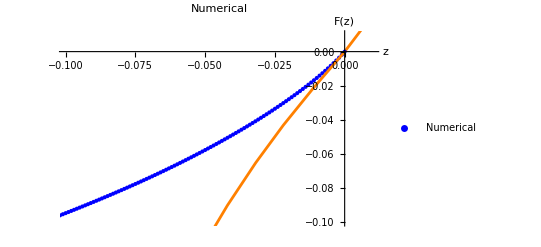

```mathematica
(*compare numerical, analytic up to 0th and 1st orders*)
Show[NumericalSol,pthsingularity,PlotRange->{{-0.1,0.01},{-0.1,0.01}}]
```

```mathematica
AnalyticSolGuess = Plot3D[(1-HeavisideTheta[x]HeavisideTheta[y-1])(-c-ProductLog[0,ψ[x]]+(x*Exp[(y-1)ProductLog[0,ψ[x]]/(ProductLog[0,ψ[x]])]/(1+ProductLog[0,ψ[x]]))),{x,-1,1},{y,0.5,1.5},PlotLabel->"guess",PlotLegends->{"guess"},AxesLabel->{"x","y","f(x, y)"}]
```

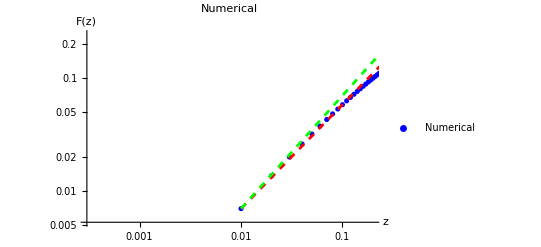

```mathematica
b=1-2(c-0.5)^2;
a=0.00703/(0.01/(1-c))^b;
b1=1-c(yMin-1)^4;
a1=0.00703/(0.01/(1-c))^b1;
(*Create the plots*)

powerLawPlot=LogLogPlot[a (x/(1-c))^b,{x,0.01,100},PlotStyle->{Red,Dashed}];
powerLawPlot1=LogLogPlot[a1 (x/(1-c))^b1,{x,0.01,100},PlotStyle->{Green,Dashed}];
Show[LogNumericalSol,powerLawPlot,powerLawPlot1]
```

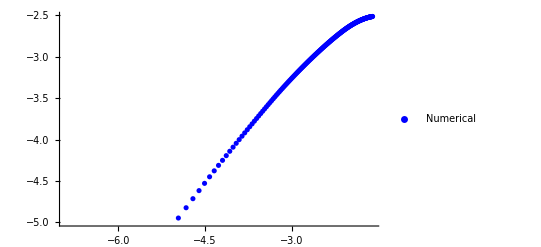

```mathematica
xValuesLog = Drop[Log[Abs[xValues]],{1,200}];
yValuesLog=Drop[Log[Abs[yValues-xValues *Log[Abs[xValues]]/Log[c]]],{1,200}];
NumericalLogSol = ListPlot[Transpose[{xValuesLog,yValuesLog}],PlotStyle->{Blue,Thick},
PlotLegends->{"Numerical"}]
```

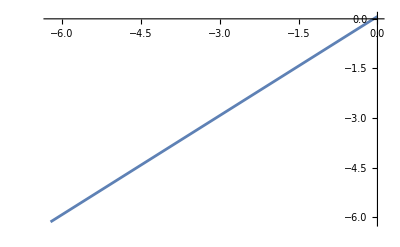

```mathematica
fit=Plot[(x-xValuesLog[[-3]])+yValuesLog[[-3]],{x,xValuesLog[[-3]],0}]
```

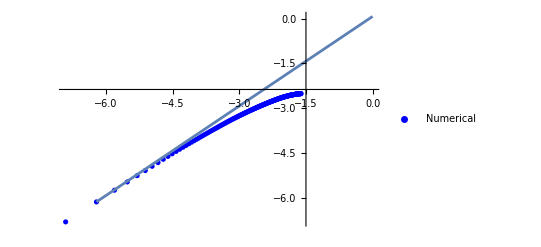

```mathematica
Show[NumericalLogSol,fit,PlotRange->All]
```

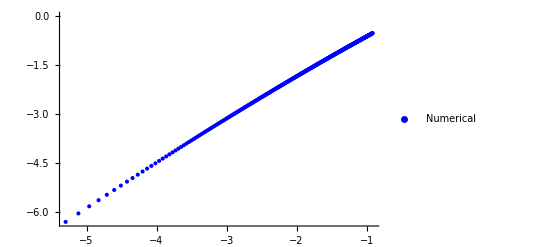

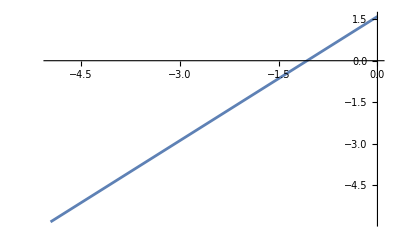

```mathematica
pxValuesLog = Drop[Log[Abs[xValues]],{-5,-1}];
pyValuesLog=Drop[Log[Abs[yValues-xValues c beta/(1-c beta)]],{-5,-1}];
pNumericalLogSol = ListPlot[Transpose[{pxValuesLog,pyValuesLog}],PlotStyle->{Blue,Thick},
PlotLegends->{"Numerical"}]
pfit=Plot[p(x-pxValuesLog[[-3]])+pyValuesLog[[-3]],{x,pxValuesLog[[-3]],0}]
```

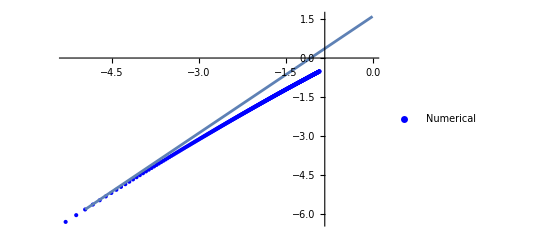

```mathematica
Show[pNumericalLogSol,pfit,PlotRange->All]
```

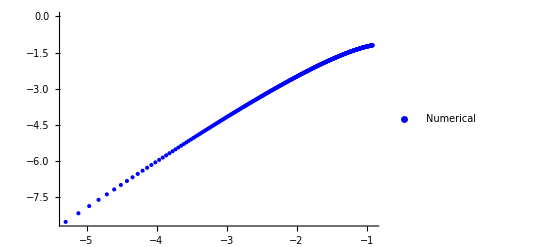

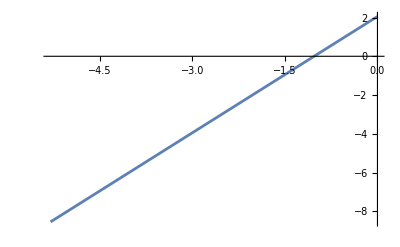

```mathematica
k2xValuesLog = Drop[Log[Abs[xValues]],{-5,-1}];
k2yValuesLog=Drop[Log[Abs[yValues-c1 xValues-c2 xValues^2 Log[Abs[xValues]]]],{-5,-1}];
k2NumericalLogSol = ListPlot[Transpose[{k2xValuesLog,k2yValuesLog}],PlotStyle->{Blue,Thick},
PlotLegends->{"Numerical"}]
k2fit=Plot[2(x-k2xValuesLog[[-1]])+k2yValuesLog[[-1]],{x,k2xValuesLog[[-1]],0}]
```

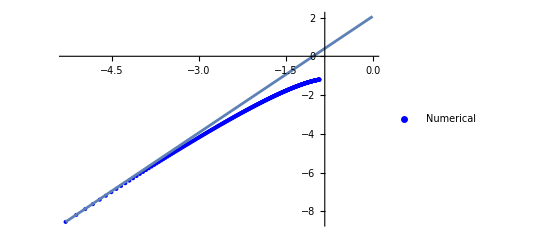

```mathematica
Show[k2NumericalLogSol,k2fit,PlotRange->All]
```